```mathematica
Table[
With[{g=MinimalGraph[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
PartitionType[SymbolToSets[symbol]]<->Length[edges]
],
{symbol,form}
]
]
]
,{k,15}
]//TableForm
```

{1,1,1,1}<->0
{2,1,1,1}<->0
{2,2,1,1}<->1
{3,2,1,1}<->2
{3,3,1,1}<->4
{4,3,1,1}<->6
{4,4,1,1}<->9
{5,4,1,1}<->12
{5,5,1,1}<->16
{6,5,1,1}<->20
{6,6,1,1}<->25
{7,6,1,1}<->30
{7,7,1,1}<->36

```mathematica
Table[
With[{g=MinimalGraph[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
Length[edges]
],
{symbol,form}
]
]
]
,{k,20}
]//TableForm
```

0
0
1
2
4
6
9
12
16
20
25
30
36
42
49
56
64
72

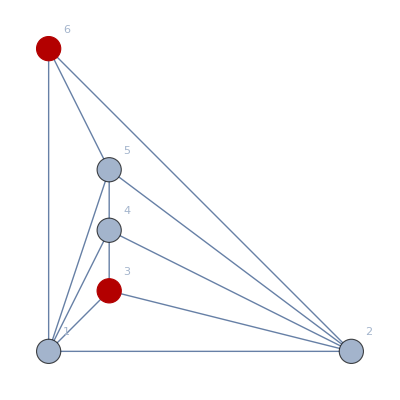
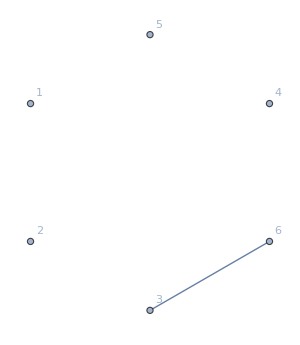
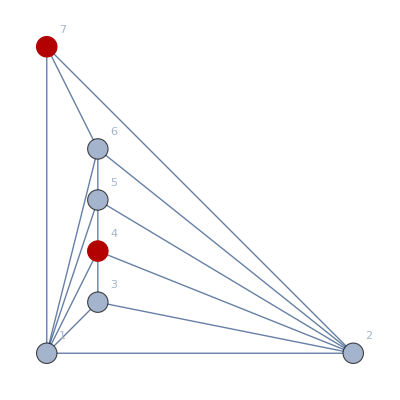
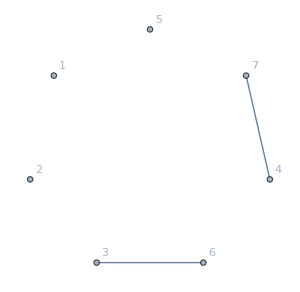
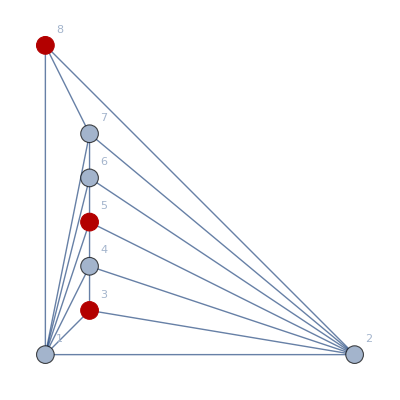
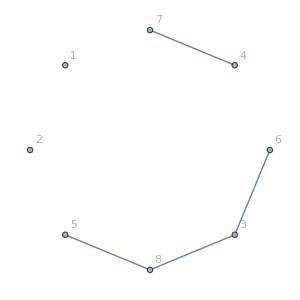
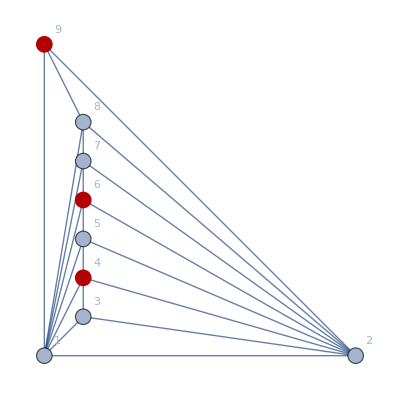
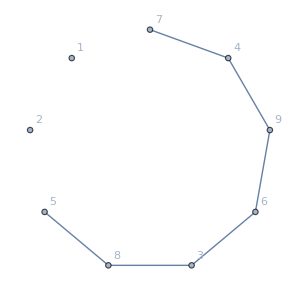
{{-Graphics-→-Graphics-6},{-Graphics-→-Graphics-7},{-Graphics-→-Graphics-8},{-Graphics-→-Graphics-9},{-Graphics-→-Graphics-10},{-Graphics-→-Graphics-11},{-Graphics-→-Graphics-12},{-Graphics-→-Graphics-13},{-Graphics-→-Graphics-14},{-Graphics-→-Graphics-15},{-Graphics-→-Graphics-16},{-Graphics-→-Graphics-17},{-Graphics-→-Graphics-18},{-Graphics-→-Graphics-19},{-Graphics-→-Graphics-20},{-Graphics-→-Graphics-21}}

```mathematica
Block[{previous={}},
Table[
With[{g=MinimalGraph[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
With[{diff=SetDifference[edges, previous]},
With[{g2=Graph[VertexList[g],edges,GraphLayout->"CircularEmbedding",GraphHighlight->diff, GraphHighlightStyle->"Thick", VertexLabels->"Name", ImageSize->300]},
previous=edges;
Graph[g,GraphHighlight->VertexList[Graph[diff]], VertexSize->Large]->Labeled[g2,Style[VertexCount[g2],Red,Bold]]
]
]
],
{symbol,form}
]
]
]
,{k,5,20}
]
]
```

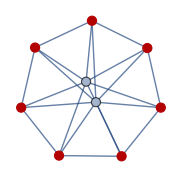
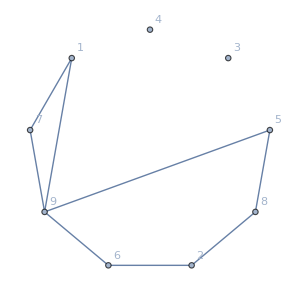
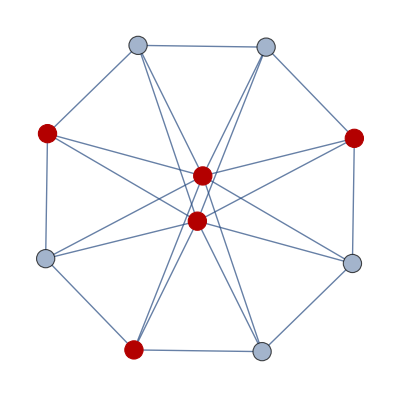
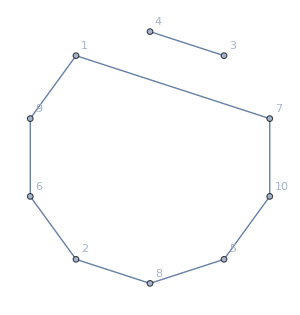
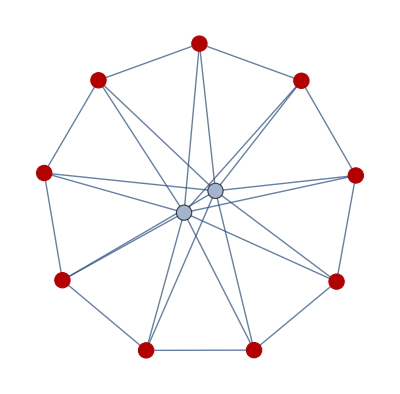
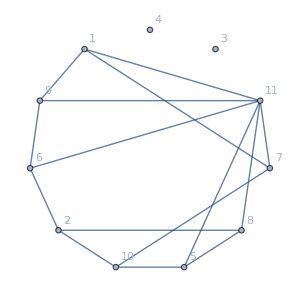
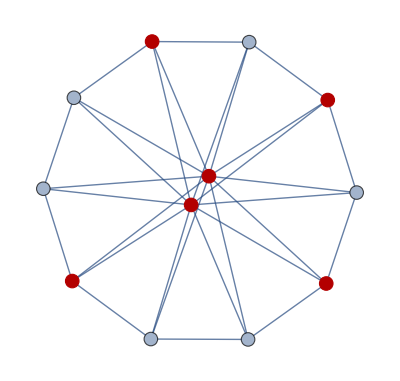
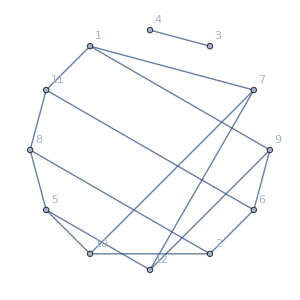
{{-Graphics-→-Graphics-9},{-Graphics-→-Graphics-10},{-Graphics-→-Graphics-11},{-Graphics-→-Graphics-12},{-Graphics-→-Graphics-13},{-Graphics-→-Graphics-14}}

```mathematica
Block[{previous={}},
Table[
With[{g=JacobsThalGraph[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
With[{diff=SetDifference[edges, previous]},
With[{g2=Graph[VertexList[g],edges,GraphLayout->"CircularEmbedding",GraphHighlight->diff, GraphHighlightStyle->"Thick", VertexLabels->"Name", ImageSize->300]},
previous=edges;
Graph[g,GraphHighlight->VertexList[Graph[diff]], VertexSize->Large]->Labeled[g2,Style[VertexCount[g2],Red,Bold]]
]
]
],
{symbol,Take[Sort[form],1]}
]
]
]
,{k,5,10}
]
]
```